```mathematica
(* Load MaTeX *)
(* See https://github.com/szhorvat/MaTeX to install *)
Get["MaTeX`"];
ConfigureMaTeX["pdfLaTeX"->"/usr/local/bin/pdflatex","Ghostscript"->"/usr/local/bin/gs"];
SetOptions[MaTeX,Magnification->1.5];
makeunit[label_,unit_]:=MaTeX[StringJoin[label,"\\ [\\textrm{",unit,"}]"]];
makeframelabel[xlabel_,xunit_,ylabel_,yunit_]:=FrameLabel->{makeunit[xlabel,xunit],makeunit[ylabel,yunit]};
```

```mathematica
(* Load CustomTicks.m from the same folder *)
Get[FileNameJoin[{NotebookDirectory[],"CustomTicks.m"}]];
SetOptions[Plot,FrameTicks->{{LinTicks,None},{LinTicks,None}}];
(* assume perry wilson's 1691 paper *)
(* Load WilsonInput.wl from the same folder *)
Get[FileNameJoin[{NotebookDirectory[],"WilsonInput.wl"}]];
```

```mathematica
lambda=c/frequency;
degreePerCell=120;
cellLength=lambda/(360/degreePerCell);
numCavity=Round[L/cellLength];
```

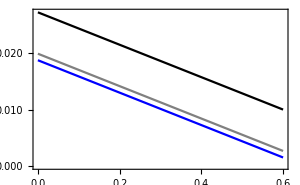

```mathematica
(* Assume constant gradient structure *)
(* 5.14 group velocity required to product constant accelearting gradient *)
vgConstantGradient[r_,L_,tau_,Q_,z_]:=omega*L/Q*(1-1/L*Quantity[z,"Meters"](1-E^(-2*tau)))/(1-E^(-2*tau))
functions={};
Do[AppendTo[functions,vgConstantGradient[r,L,tauu,Q,z]/c],{tauu,tauList}]
Plot[functions,{z,0,QuantityMagnitude[L]},Evaluate[makeframelabel["z","m","v_g","c"]],PlotStyle->plotstyle]
```

```mathematica
(* Export["/Users/user1/Desktop/cgp.pdf",%] *)
```

```mathematica
(* choose tau *)
cgTau=1;
```

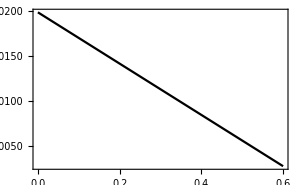

```mathematica
(* einstein beta *)
betaVg[r_,L_,tau_,Q_,z_]:=vgConstantGradient[r,L,tau,Q,z]/c;
Plot[betaVg[r,L,cgTau,Q,z],{z,0,QuantityMagnitude[L]},Evaluate[makeframelabel["z","m","\\beta",""]]]
```

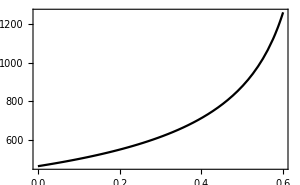

```mathematica
(* the invariant on page 10 of Hellweg Manual. Call it hellweg1. *)
hellweg1[lambda_,r_,Q_,L_,tau_,z_]:=((2*Pi*lambda*r)/(Q*betaVg[r,L,tau,Q,z]))^(1/2)
Plot[hellweg1[lambda,r,Q,L,cgTau,z],{z,0,QuantityMagnitude[L]},FrameLabel->{Evaluate[makeunit["z","m"]],MaTeX["[\\sqrt{\\Omega}]"]}]
```

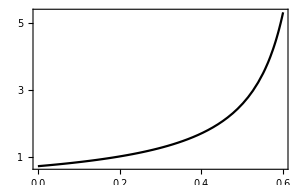

```mathematica
(* problem 5.2, alpha 1/m *)
alpha[r_,L_,tau_,Q_,z_]:=omega/(2*Q*vgConstantGradient[r,L,tau,Q,z])
Plot[alpha[r,L,cgTau,Q,z],{z,0,QuantityMagnitude[L]},Evaluate[makeframelabel["z","m","\\alpha","1/m"]]]
```

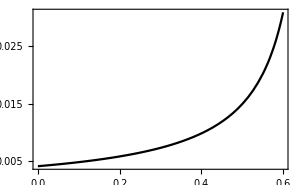

```mathematica
(* hellweg2 = alpha*lambda^(3/2). convenience function for making the table *)
hellweg2[r_,L_,tau_,Q_,z_,lambda_]:=alpha[r,L,tau,Q,z]*lambda^(3/2)
Plot[hellweg2[r,L,cgTau,Q,z,lambda],{z,0,QuantityMagnitude[L]},FrameLabel->{Evaluate[makeunit["z","m"]],MaTeX["[\\textrm{m}^{1/2}]"]}]
```

```mathematica
(* Make text file that has numCavity number of lines for HELLWEG to use in its simulation. This will make the Ohm^(1/2) and alpha*lambda^(3/2) entries. The rest needs to be filled in by you.*)
hellwegTable=Table[{QuantityMagnitude[hellweg1[lambda,r,Q,L,cgTau,z]],QuantityMagnitude[hellweg2[r,L,cgTau,Q,z,lambda]]},{z,0,QuantityMagnitude[L],QuantityMagnitude[cellLength]}];
On[Assert];
Assert[Length[hellwegTable]==numCavity];
Export[FileNameJoin[{NotebookDirectory[],"hellwegTable.txt"}],hellwegTable,"Table"];
```

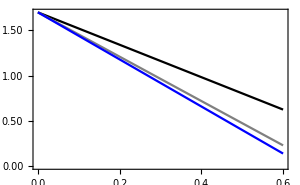

```mathematica
(* 5.12 *)
powerLconstantgradientUnloaded[pzero_,tau_]:=pzero*E^(-2*tau);
powerConstantGradientUnloaded[pzero_,tau_,z_,L_]:=pzero-(pzero-powerLconstantgradientUnloaded[pzero,tau])(Quantity[z,"Meters"]/L);
functions={};
Do[AppendTo[functions,powerConstantGradientUnloaded[pzero,tauu,z,L]/mega],{tauu,tauList}]
Plot[functions,{z,0,QuantityMagnitude[L]},Evaluate[makeframelabel["z","m","P","MW"]],PlotStyle->plotstyle]
```

```mathematica
(* Problem 5.1 filling time *)
cgFillingTime=2*cgTau*Q/omega
```

2.32743×10^-7 s

```mathematica
(* 5.18 cg vzero unloaded voltage gain of the beam after travelling from 0 to L *)
cgVZero[r_,L_,tau_,pzero_]:=(r*L*pzero)^(1/2)*(1-E^(-2*tau))^(1/2);
cgVZero[r,L,cgTau,pzero]
```

1.12695×10^7 √Ω √W

```mathematica
(* assume the beam exists *)
izero=Quantity[0.07,"Amperes"];
(* Problem 5.2 the voltage loss of the beam induced by the beam after passing through the whole linac *)
cgVBeam[r_,L_,tau_,izero_]:=1/2*r*L*izero(1-(2*tau*E^(-2*tau))/(1-E^(-2*tau)))
cgVBeam[r,L,cgTau,izero]
```

2.07738×10^6 A Ω

```mathematica
(* Eq. 5.23b the voltage gain of the beam after passing through the whole linac accounting for beam induced loss *)
vLoadedConstantGradient[r_,L_,tau_,pzero_,izero_]:=cgVZero[r,L,tau,pzero]-cgVBeam[r,L,tau,izero]
vLoadedConstantGradient[r,L,cgTau,pzero,izero]
```

9.19213×10^6 A Ω

```mathematica
(* average beam power of beam loaded structure after travelling through the entire linac, accounting for beam induced loss *)
(* energy goes up with higher tau, but power goes down *)
pAverageConstantGradient[r_,L_,tau_,pzero_,izero_,duty_]:=vLoadedConstantGradient[r,L,tau,pzero,Quantity[izero,"Amperes"]]*Quantity[izero,"Amperes"]*duty;
pAverageConstantGradient[r,L,cgTau,pzero,QuantityMagnitude[izero],duty]
```

514.759 A^2 Ω

```mathematica
functions={};
Do[AppendTo[functions,vLoadedConstantGradient[r,L,tau,pzero,Quantity[izeroo,"Amperes"]]/mega],{tau,tauList}]
vLoadedConstantGradientPlot=Plot[{functions,10},{izeroo,iZeroMin,iZeroMax},FrameLabel->{"Beam Current [A]","Voltage [MV]"},PlotStyle->plotstyledashed,PlotRange->{All,{0,22}},ImagePadding->55];
functions={};
Do[AppendTo[functions,pAverageConstantGradient[r,L,tau,pzero,izeroo,duty]],{tau,tauList}]
pAverageConstantGradientPlot=Plot[{functions,500},{izeroo,iZeroMin,iZeroMax},FrameLabel->{{None,"Beam Power [W]"},{None,None}},
Frame->{{False,True},{False,False}},
FrameTicks->{{None,LinTicks},{None,None}},
PlotRange->{All,{0,1100}},
ImagePadding->55,PlotStyle->plotstyle];
(* 60cm plotrange *)
(* 80cm 18.4 and 920 *)
```

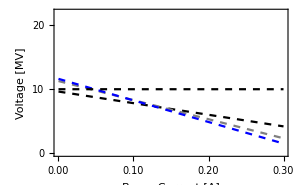
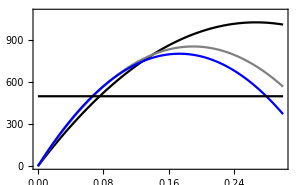

```mathematica
Overlay[{vLoadedConstantGradientPlot,pAverageConstantGradientPlot}]
```

```mathematica
(* Export["/Users/user1/Desktop/cg.pdf",%] *)
```

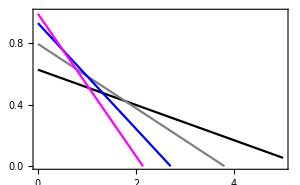

```mathematica
(* Fig 5.2 normalized net voltage gain as function of normalized beam current, as function of tau *)
iZeroFromNormalized[iNormalized_]:=iNormalized*(r*L)^(-1/2)*pzero^(1/2)
vNormalizedConstantGradient[r_,L_,tau_,pzero_,iNormalized_]:=vLoadedConstantGradient[r,L,tau,pzero,iZeroFromNormalized[iNormalized]]*(r*L*pzero)^(-1/2)
plots={vNormalizedConstantGradient[r,L,0.25,pzero,iNormalized],
vNormalizedConstantGradient[r,L,0.5,pzero,iNormalized],
vNormalizedConstantGradient[r,L,1.0,pzero,iNormalized],
vNormalizedConstantGradient[r,L,2.0,pzero,iNormalized]};
Plot[plots,{iNormalized,0,5},FrameLabel->{MaTeX["\\textrm{Normalized Beam Current }I_{0,N}"],MaTeX["\\textrm{Normalized Net Voltage Gain }V_N"]},PlotRange->{All,{0,1}},PlotStyle->{Black,Gray,Blue, Magenta}]
```

```mathematica
(* 5.9a unloaded accelerating voltage for the cg structure *)
Ea[r_,L_,tau_,Q_,pzero_, z_]:=(2*alpha[r,L,tau,Q,z]*r*powerConstantGradientUnloaded[pzero,tau,z,L])^(1/2)
```

```mathematica
Plot[Ea[r,L,cgTau,Q,pzero,z]/mega,{z,0,QuantityMagnitude[L]},Evaluate[makeframelabel["z","m","E_a","MV/m"]]]
```

-Graphics-

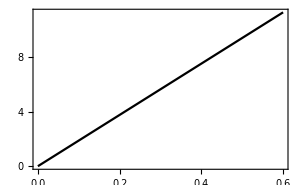

```mathematica
(* V0 the unloaded net voltage gain of a particle that has travelled z meters through the linac *)
Plot[Integrate[Ea[r,L,cgTau,Q,pzero,zVariable]/mega,{zVariable,0,z}],{z,0,QuantityMagnitude[L]},Evaluate[makeframelabel["z","m","V_0","MV"]]]
```

```mathematica
(* V0 the unloaded net voltage gain of particle that has travelled through the whole linac *)
Integrate[Ea[r,L,cgTau,Q,pzero,z],{z,0,QuantityMagnitude[L]}]
```

1.12695×10^7 V/m

```mathematica
(* beam-induced accelerating field that acts against the accelerating voltage from the RF source. Problem 5.2 *)
Ebeam[izero_,r_,L_,tau_,z_]:=izero*r*(1-(1-(Quantity[z,"Meters"]/L)*(1-E^(-2*tau)))^(1/2))
(* the beam induced accelerating field at the start of the linac. should be zero because assume the beam is stationary at the start of the linac. *)
Ebeam[izero,r,L,cgTau,0]
```

0. A Ω/m

```mathematica
(* the beam induced accelerating field at the end of the linac *)
Ebeam[izero,r,L,cgTau,QuantityMagnitude[L]]
```

6.37178×10^6 A Ω/m

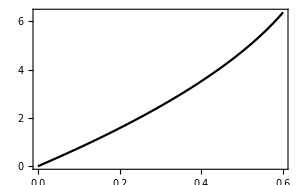

```mathematica
(* the beam induced accelerating field as it travels down the linac *)
Plot[Ebeam[izero,r,L,cgTau,z]/mega,{z,0,QuantityMagnitude[L]},Evaluate[makeframelabel["z","m","E_b","MV/m"]]]
```

```mathematica
(* the beam induced accelerating field at the end of the linac *)
Ebeam[izero,r,L,cgTau,QuantityMagnitude[L]]
```

6.37178×10^6 A Ω/m

```mathematica
(* the voltage change induced by the beam that acts directly against the voltage gain, after passing through the entire structure *)
Integrate[Ebeam[izero,r,L,cgTau,z],{z,0,QuantityMagnitude[L]}]
```

1.61708×10^6 V/m

```mathematica
(* E the accelerating field through the structure accounting for beam induced accelerating field *)
EaLoaded[izero_,r_,L_,tau_,Q_,pzero_,z_]:=Ea[r,L,tau,Q,pzero,z]-Ebeam[izero,r,L,tau,z]
(* the accelerating field at the start of the linac accounting for beam induced accelerating field *)
EaLoaded[izero,r,L,cgTau,Q,pzero,0]
```

1.87825×10^7 A Ω/m

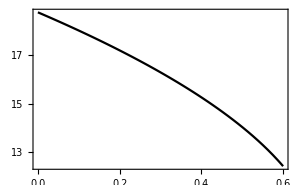

```mathematica
Plot[EaLoaded[izero,r,L,cgTau,Q,pzero,z]/mega,{z,0,QuantityMagnitude[L]},Evaluate[makeframelabel["z","m","E","MV/m"]]]
```

```mathematica
(* the voltage gain of the electrons through the whole linac accounting for beam loading *)
Integrate[EaLoaded[izero,r,L,cgTau,Q,pzero,z],{z,0,QuantityMagnitude[L]}]
```

9.65243×10^6 V/m

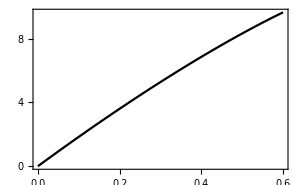

```mathematica
(* the voltage gain of the beam as it passes through the linac accounting for the beam induced voltage. multiply by e to get the energy of the beam as it passes through the linac. *)
Plot[Integrate[EaLoaded[izero,r,L,cgTau,Q,pzero,zVariable],{zVariable,0,z}]/mega,{z,0,QuantityMagnitude[L]},Evaluate[makeframelabel["z","m","V","MV"]]]
```